```mathematica
(* Available Plays:
1. Antigone
2. Death of a Salesman
3-22. Hamlet
23-48. King Lear
49-57. Midsummer Night's Dream
58. Oedipus At Colonus
59. Oedipus The King
60-83. Romeo and Juliet
84. The Glass Menagerie
85-93 The Tempest *)
(* play#, negativitybias, positive tolerance, negative tolerance, startInd, endInd *)
plays={"Antigone", "Death of a Salesman", "Hamlet", "King Lear", "Midsummer Night's Dream", "Oedipus At Colonus", "Oedipus The King", "Romeo and Juliet", "The Glass Menagerie", "The Tempest"};
playConditions=Table[plays⟦i⟧->{i,1,.30,-.30},{i,1,Length[plays]}];
exceptions={
Values[playConditions⟦1⟧]->{1,1.2,.20,-.30},
Values[playConditions⟦2⟧]->{2,1.35,.30,-.20},
Values[playConditions⟦3⟧]->{3,1.25,.40,-.30},
Values[playConditions⟦4⟧]->{4,1.3,.30,-.30},
Values[playConditions⟦5⟧]->{5,1.3,.30,-.30},
Values[playConditions⟦6⟧]->{6,1.3,.30,-.30},
Values[playConditions⟦7⟧]->{7,1.3,.30,-.30},
Values[playConditions⟦8⟧]->{8,1.3,.35,-.30},
Values[playConditions⟦9⟧]->{9,1.3,.30,-.20},
Values[playConditions⟦10⟧]->{10,1.3,.30,-.30}};
playConditions=playConditions/.exceptions;
playNum=8;
```

```mathematica
(* Process Plays *)
SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]];
text=StringJoin[Import[#]&/@files⟦60;;83⟧];
speakerOrder=Capitalize[ToLowerCase@StringCases[text,Shortest["<b>"~~x__~~"</b>"]->x]//Flatten,"AllWords"];
nameList=speakerOrder//DeleteDuplicates;
```

```mathematica
(* Separates lines of text ready for sentiment analysis *)
lines=StringSplit[text//StringDelete[Shortest["<i>"~~x__~~"</i>"]]//StringDelete[Shortest["["~~x__~~"]"]],Shortest["<b>"~~x__~~"</b>"]]//StringDelete[Shortest["<"~~x___~~">"]]//Rest;
sentences=lines//TextSentences;
lineLength=Length/@sentences;
```

```mathematica
(* Create directed edges for graph *)
speakerBySentence=Table[Table[speakerOrder⟦i⟧,Length[sentences⟦i⟧]],{i,1,Length[lines]}]//Flatten;
recipientByLine=Prepend[Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}],Table[speakerOrder⟦2⟧,Length[First[sentences]]]];
recipientBySentence=Nest[Prepend[speakerOrder⟦2⟧],Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}]//Flatten,Length[First[sentences]]];

emphasis=WordFrequency[Flatten[sentences],#,IgnoreCase->True]&/@nameList;
diffRecipientPos=SortBy[Position[emphasis,_?Positive],Last];

brokenInd=TakeList[Range[Length[recipientBySentence]],lineLength];
sentenceToLineRules=Table[i->First@@Position[brokenInd,i],{i,1,Length[recipientBySentence]}];
lineIndOfSentences=Range[Length[recipientBySentence]]/.sentenceToLineRules;
sentenceNumOfDiffLine[x_]:=Last@diffRecipientPos⟦x⟧-Total[lineLength⟦;;lineIndOfSentences⟦Last@diffRecipientPos⟦x⟧⟧-1⟧];

For[i=1,i≤Length[diffRecipientPos],i++,
recipientByLine⟦lineIndOfSentences⟦Last@diffRecipientPos⟦i⟧⟧,sentenceNumOfDiffLine[i];;⟧=nameList⟦First@diffRecipientPos⟦i⟧⟧]

recipientBySentence=recipientByLine//Flatten;
finalRules=Table[speakerBySentence⟦i⟧->recipientBySentence⟦i⟧,{i,1,Length[speakerBySentence]}];
ruleList=DeleteCases[DeleteDuplicates[finalRules],x_->x_];
```

```mathematica
(* Implement Sentiment Analysis of lines *)
feelings=Classify["Sentiment",#,"Probabilities"]&/@sentences//Flatten;
```

```mathematica
(* Put sentiment into edges *)
{pos,neu,neg}=Table[feelings⟦i⟧[#],{i,1,Length[feelings]}]&/@{"Positive","Neutral","Negative"};
negBias=Values[playConditions]⟦playNum⟧⟦2⟧;
Health=(pos-negBias*neg)/(1+neu);
sentenceHealth={finalRules⟦#⟧,Health⟦#⟧}&/@Range[Length[Health]];
sentenceHealthFormat=Cases[sentenceHealth,{#,_}]&/@ruleList;
relationshipHealth=Table[Mean[Table[sentenceHealthFormat⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sentenceHealthFormat⟦i⟧]}]],{i,1,Length[sentenceHealthFormat]}];
```

```mathematica
(* Incorporate Frequency for into Health *)
freq=Table[Length[sentenceHealthFormat⟦i⟧],{i,1,Length[sentenceHealthFormat]}];
freqMultiplier[x_]:=(Log[x]+2)/2;
thickness=N[freq]/Max[N[freq]]*.012;
edgeWidth=Table[ruleList⟦i⟧->freqMultiplier[N[freq⟦i⟧]],{i,Length[ruleList]}];
```

```mathematica
(* Exclude Neutral/Conflicted Relationships *)
relationshipHealthFinal=relationshipHealth*N[freqMultiplier[freq]];
posTolerance=Values[playConditions]⟦playNum⟧⟦3⟧;
negTolerance=Values[playConditions]⟦playNum⟧⟦4⟧;

viableEdges=Position[relationshipHealthFinal,x_/;x>posTolerance||x<negTolerance]//Flatten;
relationshipHealthFinalExc=Table[relationshipHealthFinal⟦i⟧,{i,viableEdges}];
viableFreq=Table[freq⟦i⟧,{i,viableEdges}];
viableThickness=Table[thickness⟦i⟧,{i,viableEdges}];
viableEdgeWidth=Table[edgeWidth⟦i⟧,{i,viableEdges}];
```

```mathematica
(* Modify the Graph with color (health) and width (frequency) *)
relationshipColors=Table[Blend[{Red,Gray,Green},(i+1)/2],{i,relationshipHealthFinalExc}]
```

{RGBColor[0.6941539972659202, 0.3058460027340798, 0.3058460027340798],RGBColor[0.23133466078127318, 0.7686653392187268, 0.23133466078127318],RGBColor[0.8055524800981826, 0.1944475199018174, 0.1944475199018174],RGBColor[0.04721401330291264, 0.9527859866970874, 0.04721401330291264],RGBColor[0.013206147624287956, 0.986793852375712, 0.013206147624287956],RGBColor[0.6888034844987115, 0.31119651550128846, 0.31119651550128846],RGBColor[0.26606589260761093, 0.7339341073923891, 0.26606589260761093],RGBColor[0.2053070091301059, 0.7946929908698941, 0.2053070091301059],RGBColor[0.17080607799362868, 0.8291939220063713, 0.17080607799362868],RGBColor[0.2756756957691694, 0.7243243042308306, 0.2756756957691694],RGBColor[0.036508926529734254, 0.9634910734702657, 0.036508926529734254],RGBColor[0.07243473079208806, 0.9275652692079119, 0.07243473079208806],RGBColor[0.25052955337663174, 0.7494704466233683, 0.25052955337663174],RGBColor[0.3085793115549992, 0.6914206884450008, 0.3085793115549992],RGBColor[0.257235107363853, 0.742764892636147, 0.257235107363853],RGBColor[0.09936303017910086, 0.9006369698208991, 0.09936303017910086],RGBColor[0.19054218164321401, 0.809457818356786, 0.19054218164321401],RGBColor[0.24181612946347975, 0.7581838705365203, 0.24181612946347975],RGBColor[0.24304575034030007, 0.7569542496596999, 0.24304575034030007],RGBColor[0.23704471155524676, 0.7629552884447532, 0.23704471155524676],RGBColor[0.16278197044861198, 0.837218029551388, 0.16278197044861198],RGBColor[0.6822035744382041, 0.3177964255617959, 0.3177964255617959],RGBColor[0.2927661129034339, 0.7072338870965661, 0.2927661129034339],RGBColor[0.019082434749944976, 0.980917565250055, 0.019082434749944976],RGBColor[0.3219625804638381, 0.6780374195361619, 0.3219625804638381],RGBColor[0.1741627814417026, 0.8258372185582974, 0.1741627814417026],RGBColor[0.27115611980434773, 0.7288438801956523, 0.27115611980434773],RGBColor[0.24419941835671843, 0.7558005816432816, 0.24419941835671843],RGBColor[0.1576597443175476, 0.8423402556824524, 0.1576597443175476],RGBColor[0.19028371489119822, 0.8097162851088018, 0.19028371489119822],RGBColor[0.30341000032860777, 0.6965899996713922, 0.30341000032860777],RGBColor[0.31774954744721784, 0.6822504525527822, 0.31774954744721784],RGBColor[0.2303678403597078, 0.7696321596402922, 0.2303678403597078],RGBColor[0.19402800727845992, 0.8059719927215401, 0.19402800727845992],RGBColor[0.053374052643665015, 0.946625947356335, 0.053374052643665015],RGBColor[0., 1., 0.],RGBColor[0.11352619441316336, 0.8864738055868366, 0.11352619441316336],RGBColor[0.24738436976884182, 0.7526156302311582, 0.24738436976884182],RGBColor[0.27849262245985207, 0.7215073775401479, 0.27849262245985207],RGBColor[0.2182165943357497, 0.7817834056642503, 0.2182165943357497],RGBColor[0.66471828574426, 0.33528171425574005, 0.33528171425574005],RGBColor[0., 1., 0.],RGBColor[0., 1., 0.],RGBColor[0.2123770393350295, 0.7876229606649705, 0.2123770393350295],RGBColor[0.2541547739502086, 0.7458452260497914, 0.2541547739502086],RGBColor[0., 1., 0.],RGBColor[0.21430592065803988, 0.7856940793419601, 0.21430592065803988],RGBColor[0.09328453384636615, 0.9067154661536339, 0.09328453384636615],RGBColor[0.26807184152201224, 0.7319281584779878, 0.26807184152201224],RGBColor[0.12762876035671367, 0.8723712396432863, 0.12762876035671367],RGBColor[0.18291630433716732, 0.8170836956628327, 0.18291630433716732],RGBColor[0.25428521277324156, 0.7457147872267584, 0.25428521277324156],RGBColor[1., 0., 0.],RGBColor[0.2698001432784911, 0.7301998567215089, 0.2698001432784911],RGBColor[0., 1., 0.],RGBColor[0.6636011239045507, 0.3363988760954493, 0.3363988760954493],RGBColor[0.8841928540746647, 0.11580714592533525, 0.11580714592533525],RGBColor[0.19590289430160313, 0.8040971056983969, 0.19590289430160313],RGBColor[0.29505117104277045, 0.7049488289572295, 0.29505117104277045],RGBColor[0.6772353687866396, 0.3227646312133604, 0.3227646312133604],RGBColor[0.652621098750578, 0.34737890124942195, 0.34737890124942195],RGBColor[0.1366797261225493, 0.8633202738774507, 0.1366797261225493],RGBColor[0.2764615528964809, 0.7235384471035191, 0.2764615528964809],RGBColor[0.7934339000471168, 0.20656609995288322, 0.20656609995288322],RGBColor[0., 1., 0.],RGBColor[0.7322135727594983, 0.2677864272405017, 0.2677864272405017],RGBColor[0.09185735163604902, 0.908142648363951, 0.09185735163604902],RGBColor[0.06217229069000907, 0.9378277093099909, 0.06217229069000907],RGBColor[0.2574812824123974, 0.7425187175876026, 0.2574812824123974],RGBColor[0.32116380969211566, 0.6788361903078843, 0.32116380969211566],RGBColor[0.23965470604450645, 0.7603452939554936, 0.23965470604450645],RGBColor[0.6834920042724538, 0.3165079957275462, 0.3165079957275462],RGBColor[0., 1., 0.],RGBColor[1., 0., 0.],RGBColor[0.2995453501581369, 0.7004546498418631, 0.2995453501581369],RGBColor[1., 0., 0.]}

```mathematica
viableRules=Table[ruleList⟦i⟧,{i,viableEdges}];
edgeColors=Table[viableRules⟦i⟧->relationshipColors⟦i⟧,{i,Length[viableRules]}];
```

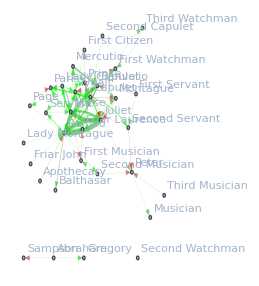

-Graphics-

```mathematica
edgeThickness=Thread[viableRules->(Thickness[#]&/@viableThickness)];
edgeFormat=Table[viableRules⟦i⟧->Directive[Values[edgeThickness]⟦i⟧,Values[edgeColors]⟦i⟧],{i,1,Length[edgeColors]}];
g=Graph[nameList,viableRules,VertexLabels->All,EdgeStyle->edgeFormat]
cgp=CommunityGraphPlot[g,ImageSize->800,VertexLabelStyle->14]
```